```mathematica
(*raw = ImportString["-40.0, 802.5501649025324, 9.897063209304143e-06, 1.6442387355664674e-05, 5.64355741101242e-06, 3.78576789775162e-06
-39.5, 866.533851643425, 9.817927815280411e-06, 1.627662058099651e-05, 5.593817474662108e-06, 3.7525955013308354e-06
-39.0, 941.4978573578746, 9.721689654509931e-06, 1.6093470997200626e-05, 5.5318282401617054e-06, 3.730760026438583e-06
-38.5, 1022.4355540002215, 9.58183743126413e-06, 1.5891491321845548e-05, 5.4892523367019735e-06, 3.6963664210779994e-06
-38.0, 1129.3214165617476, 9.449740667238964e-06, 1.569245341903351e-05, 5.437753323358104e-06, 3.6725960264269596e-06
-37.5, 1274.8481996193761, 9.329607142017544e-06, 1.5499202322323485e-05, 5.416531005225476e-06, 3.6588217162109133e-06
-37.0, 1447.3348168726684, 9.160027762556977e-06, 1.5288400014041147e-05, 5.371278915075637e-06, 3.6300782773395963e-06
-36.5, 1617.1737173827341, 8.989912666881602e-06, 1.5111289837444963e-05, 5.341044636122241e-06, 3.619600363603868e-06
-36.0, 1893.374106492834, 8.868542210689083e-06, 1.4960323230936067e-05, 5.322207865278337e-06, 3.6204754151520485e-06
-35.5, 2321.1885818720225, 8.697211702653587e-06, 1.4828167236660004e-05, 5.307494104631518e-06, 3.632014277695204e-06
-35.0, 2785.514712158881, 8.602667792441985e-06, 1.4741329385845e-05, 5.331079911540165e-06, 3.670890529417544e-06
-34.5, 3511.8937495640494, 8.528293661226198e-06, 1.4673269127548375e-05, 5.372317835064762e-06, 3.7384079386313507e-06
-34.0, 4978.243861381265, 8.575271201101044e-06, 1.4699800146543813e-05, 5.536240523510627e-06, 3.939252972462688e-06
-33.5, 8044.462533678551, 8.946793801985541e-06, 1.5074334016692546e-05, 6.035500387380982e-06, 4.467367894046379e-06
-33.0, 18864.329212802524, 1.1001567088251676e-05, 1.7381066929652282e-05, 8.156763779570048e-06, 6.7602257463992465e-06
-32.5, 128074.59543473764, 2.067788714436715e-05, 3.289784746375367e-05, 1.8951237694194655e-05, 1.8678227754585627e-05
-32.0, 72528.56322566787, 1.4642739420049869e-05, 2.129107682366626e-05, 1.1912449358191821e-05, 1.0990149027693446e-05
-31.5, 55128.144987555934, 1.118265220913902e-05, 1.7269429187655525e-05, 8.432198457647417e-06, 7.310068445915477e-06
-31.0, 41811.528336419855, 1.072015420328209e-05, 1.652772106175418e-05, 7.548487081088023e-06, 6.190944452926688e-06
-30.5, 33562.92503472073, 9.6073193201778e-06, 1.5355388089232145e-05, 6.562588240817345e-06, 5.05534007734426e-06"];
raw = raw~Join~ImportString["-40.0, 804.5788660302463, 9.907014968174734e-06, 1.644398077182487e-05, 5.641478853225166e-06, 3.78001908564204e-06
-39.8, 826.421107430282, 9.884564806447121e-06, 1.6380580161504154e-05, 5.627764397915139e-06, 3.7765292872716937e-06
-39.599999999999994, 854.7107605280509, 9.824286955958193e-06, 1.6308872148953785e-05, 5.599361155409357e-06, 3.7586561488869975e-06
-39.39999999999999, 885.446416841385, 9.791261882001797e-06, 1.6239599530995248e-05, 5.579072602272419e-06, 3.74668954761546e-06
-39.19999999999999, 912.1331923766148, 9.771286557100148e-06, 1.616698843984193e-05, 5.559091680474743e-06, 3.742193332974814e-06
-38.999999999999986, 937.5647801738596, 9.70698066785564e-06, 1.6089939802926322e-05, 5.5304859477421235e-06, 3.7277925842176065e-06
-38.79999999999998, 976.3349124741184, 9.65876184148271e-06, 1.601307039144697e-05, 5.515325172325863e-06, 3.711017393529097e-06
-38.59999999999998, 999.7576448811561, 9.592465764144511e-06, 1.5935077817480428e-05, 5.501092954182769e-06, 3.7084658584563125e-06
-38.39999999999998, 1058.0641841604986, 9.571244779553452e-06, 1.5861996199181628e-05, 5.482793279959166e-06, 3.695344325220293e-06
-38.199999999999974, 1096.2245042746615, 9.519880105699309e-06, 1.578295406444356e-05, 5.473085300402355e-06, 3.6879852026218e-06
-37.99999999999997, 1162.5822945421871, 9.471892672905179e-06, 1.568899364529667e-05, 5.43822616809663e-06, 3.6738200798765825e-06
-37.79999999999997, 1202.9306825492768, 9.385968978421847e-06, 1.560855916732964e-05, 5.416155631681629e-06, 3.6609870021961727e-06
-37.599999999999966, 1238.6507015101233, 9.330107883059366e-06, 1.5540855260383043e-05, 5.4185215063778374e-06, 3.65995251306626e-06
-37.39999999999996, 1301.789662090478, 9.282562574170552e-06, 1.5448193974225407e-05, 5.395645922507171e-06, 3.6467459968993895e-06
-37.19999999999996, 1360.457664810563, 9.21552994692798e-06, 1.537882568826831e-05, 5.387400030049496e-06, 3.644598891927563e-06
-36.99999999999996, 1436.9087234580961, 9.16768845425782e-06, 1.529288091555964e-05, 5.372090669864582e-06, 3.6336678951583233e-06
-36.799999999999955, 1505.3051598605034, 9.090088118798394e-06, 1.5207428317876194e-05, 5.353873473368823e-06, 3.621577032586568e-06
-36.59999999999995, 1608.281661373711, 9.028818886678317e-06, 1.5157138815093307e-05, 5.358261375313192e-06, 3.6372057612836096e-06
-36.39999999999995, 1670.3501270000352, 8.952283293972777e-06, 1.5071639951667898e-05, 5.330285450305018e-06, 3.6102180459064094e-06
-36.199999999999946, 1786.7022867814471, 8.896719080560917e-06, 1.4999600942282393e-05, 5.3141511159631795e-06, 3.605913811413076e-06
-35.99999999999994, 1928.7127442918493, 8.85418390482334e-06, 1.4958526420916593e-05, 5.324799848169658e-06, 3.6200685030429446e-06
-35.79999999999994, 2027.4478946028498, 8.767682739278191e-06, 1.4899745612206009e-05, 5.311311390211412e-06, 3.6154971940054453e-06
-35.59999999999994, 2218.6201203854007, 8.729943770387196e-06, 1.4850280837158006e-05, 5.309577698866841e-06, 3.626807464504313e-06
-35.399999999999935, 2313.401806755261, 8.672046206136147e-06, 1.4812060061853347e-05, 5.3134697554775204e-06, 3.6392192045807186e-06
-35.19999999999993, 2514.090709796664, 8.624352252956214e-06, 1.476171960650899e-05, 5.309790045439719e-06, 3.639764618584971e-06
-34.99999999999993, 2761.2766026944673, 8.59678721332305e-06, 1.4739218954204918e-05, 5.330634089389022e-06, 3.6703369384469545e-06
-34.799999999999926, 3098.8467676574087, 8.574881804458335e-06, 1.4704369565416937e-05, 5.340260221343421e-06, 3.699550709585297e-06
-34.59999999999992, 3489.097450158401, 8.536653110293324e-06, 1.4672584216170803e-05, 5.353338281100978e-06, 3.7229423043103216e-06
-34.39999999999992, 3790.4861288372463, 8.54903725298416e-06, 1.4663269400917854e-05, 5.388887044697597e-06, 3.763524635542908e-06
-34.19999999999992, 4316.304474300229, 8.549201946356807e-06, 1.4687120470882482e-05, 5.462169730153357e-06, 3.8555436423954825e-06
-33.999999999999915, 4983.47996469744, 8.572993026048098e-06, 1.46995032516016e-05, 5.53361133311302e-06, 3.935964255910948e-06
-33.79999999999991, 5835.239240445556, 8.609473966029539e-06, 1.4752677378297978e-05, 5.63873889645363e-06, 4.055841322339752e-06
-33.59999999999991, 7315.484414354937, 8.76804360744353e-06, 1.4929436036154786e-05, 5.874516476149831e-06, 4.300589409048515e-06
-33.399999999999906, 9294.82258158502, 9.144488017075413e-06, 1.52663177604465e-05, 6.2527015715763155e-06, 4.679475597846744e-06
-33.1999999999999, 12245.43748547099, 9.782252274023815e-06, 1.5906050226548455e-05, 6.878344223558166e-06, 5.327845750096603e-06
-32.9999999999999, 19194.714680361707, 1.100534120139613e-05, 1.73799502024736e-05, 8.152169357344278e-06, 6.771069246348891e-06
-32.7999999999999, 41892.41048732316, 1.3392954612866902e-05, 2.086439202600408e-05, 1.075744316619897e-05, 9.758281197428946e-06
-32.599999999999895, 226663.61797855195, 1.8135395068253605e-05, 2.856470999547454e-05, 1.607800317658501e-05, 1.5604382743431185e-05
-32.39999999999989, 107240.59663268963, 2.208449717268814e-05, 3.463949538367448e-05, 2.025269140291382e-05, 1.9909762495788387e-05
-32.19999999999989, 84933.5987593615, 2.0165942549387407e-05, 2.9495739323018287e-05, 1.742145318383044e-05, 1.6654442385766393e-05
-31.999999999999886, 72135.6062921998, 1.4672027885779793e-05, 2.129623932649481e-05, 1.191467977143259e-05, 1.1001439700497927e-05
-31.799999999999883, 64201.67826871009, 1.1896650086928913e-05, 1.7814976220357253e-05, 9.211573937666646e-06, 8.235242499110642e-06
-31.59999999999988, 55160.663790712315, 1.1047531469487776e-05, 1.7226913055957312e-05, 8.48140007907868e-06, 7.43248200250538e-06
-31.399999999999878, 48906.1273070476, 1.1234122306621097e-05, 1.722377708623491e-05, 8.335533279355888e-06, 7.141989180120241e-06
-31.199999999999875, 45698.31228743233, 1.1057977707054971e-05, 1.694547040097452e-05, 7.98894592861763e-06, 6.683917974470146e-06
-30.999999999999872, 40313.8463654964, 1.0721916577268602e-05, 1.6529018232818684e-05, 7.558575963484184e-06, 6.192338906521701e-06"];*)

(*raw = ImportString["-40.0, 2127.717629298316, 9.42623044420731e-05, 1.0438745676109476e-05, 1.5554167620247574e-05, 5.491987665100373e-06, 3.890271575214626e-06
-39.5, 2538.5658473383196, 8.41106365955537e-05, 1.0281056503731871e-05, 1.5355488044042816e-05, 5.471500750509116e-06, 3.900732103464178e-06
-39.0, 3001.1307674017917, 7.41542916803063e-05, 1.0237482134809502e-05, 1.5246100850009493e-05, 5.50910112027534e-06, 3.91042397386869e-06
-38.5, 3397.9225373140916, 6.438488115575994e-05, 1.0206294313251806e-05, 1.5172820629077136e-05, 5.555660858823306e-06, 3.9488703908882385e-06
-38.0, 4618.993692713818, 5.4668690381079296e-05, 1.0087625705948138e-05, 1.5159276917440181e-05, 5.6390126776241666e-06, 4.051203757027302e-06
-37.5, 6527.793386725876, 4.5068303276503435e-05, 1.012592613879307e-05, 1.5202493877246107e-05, 5.8126135846207856e-06, 4.233643972701708e-06
-37.0, 9752.20033799562, 3.5582076070713645e-05, 1.0412189671643717e-05, 1.5434641195140895e-05, 6.151091510517564e-06, 4.574584350298858e-06
-36.5, 18696.305055794644, 2.624595720107365e-05, 1.1363957529224824e-05, 1.624918581481682e-05, 7.037742994924315e-06, 5.561960141539715e-06
-36.0, 55694.27704183554, 1.7038330418623443e-05, 1.5456166131788985e-05, 2.0762256184633032e-05, 1.0840253060280634e-05, 9.815254153511625e-06
-35.5, 124713.40150055518, 8.011324134893627e-06, 3.2413866350283874e-05, 4.635707666918857e-05, 2.6937910288600286e-05, 2.6841174128564577e-05
-35.0, 62558.8275153312, 5.314965164502602e-06, 2.0178999472461973e-05, 2.8947150169359463e-05, 1.6642105193608206e-05, 1.6021803871083765e-05
-34.5, 44008.48726502721, 1.1703718115064442e-05, 1.2749363560775626e-05, 2.04671880235954e-05, 1.01562347807763e-05, 8.779111920253732e-06
-34.0, 28426.606688911863, 1.8985941441393537e-05, 9.782714625401081e-06, 1.7145945566332843e-05, 7.651650782765942e-06, 5.992406727782711e-06
-33.5, 33726.94318211473, 2.6194751717543613e-05, 8.647720152025787e-06, 1.567620662787285e-05, 6.531518325215329e-06, 4.796167186590204e-06
-33.0, 24384.88666352144, 3.352363483779816e-05, 7.967165565686676e-06, 1.4890087662730548e-05, 5.9059460560999624e-06, 4.1941617653255865e-06
-32.5, 16446.1278442149, 4.084519182868359e-05, 7.34817702630561e-06, 1.4474900836106098e-05, 5.548672200236935e-06, 3.905263525827678e-06
-32.0, 19419.441920943045, 4.8151136562101186e-05, 7.114281685003857e-06, 1.4196504435247155e-05, 5.364457025971064e-06, 3.7300686905493295e-06
-31.5, 23083.50155882636, 5.540844513578442e-05, 7.164899778427366e-06, 1.3965968613040325e-05, 5.229236672935969e-06, 3.6043299121880113e-06
-31.0, 24768.01902232212, 6.264493634340328e-05, 7.126296268527869e-06, 1.3774828024729263e-05, 5.116038125264864e-06, 3.5031559509772912e-06
-30.5, 19193.968647080193, 7.015422801661169e-05, 7.216623462548582e-06, 1.36073866396442e-05, 5.013897659532941e-06, 3.4118913490169086e-06"];*)




raw = ImportString["-40.0, 1839.832001882797, 9.341394304555081e-05, 1.0249687814667741e-05, 1.5300749689801167e-05, 5.483148357706039e-06, 3.87257604530159e-06
-39.5, 2125.2362578232646, 8.329056188280936e-05, 1.0152004550526597e-05, 1.512395817663971e-05, 5.486403283048751e-06, 3.871776813944137e-06
-39.0, 2468.7611276987877, 7.335722532757104e-05, 1.0045946266274806e-05, 1.4965058027026411e-05, 5.504766152150957e-06, 3.879698685563202e-06
-38.5, 2891.163287077533, 6.352811771033222e-05, 9.904427503105043e-06, 1.4868729658757796e-05, 5.540557624061913e-06, 3.917490512860975e-06
-38.0, 3703.411289465376, 5.387996445994699e-05, 9.884702023486786e-06, 1.4840537713083507e-05, 5.625986585985892e-06, 4.017453199536896e-06
-37.5, 4755.8784833602385, 4.436455490991653e-05, 9.985487316694427e-06, 1.4907949457832468e-05, 5.793182057536245e-06, 4.207844629972622e-06
-37.0, 6741.873673373427, 3.4986587548404976e-05, 1.0250176329773543e-05, 1.512488909569923e-05, 6.136369767375499e-06, 4.5764761912326984e-06
-36.5, 11501.640312701595, 2.5666849907816618e-05, 1.1246018629176302e-05, 1.6042719857335334e-05, 7.154408844710321e-06, 5.670342844317117e-06
-36.0, 36966.60911104648, 1.6490971782973942e-05, 1.576346112931766e-05, 2.16151104227336e-05, 1.1605063238303486e-05, 1.0890654074829596e-05
-35.5, 114654.80995672909, 7.4219832362668865e-06, 3.2905541631691874e-05, 4.503705867909287e-05, 2.6844901250674312e-05, 2.6595256590756128e-05
-35.0, 67252.0954354459, 6.189679796902039e-06, 1.691521585232436e-05, 2.343089112144462e-05, 1.3461215590631422e-05, 1.2511958180386693e-05
-34.5, 47711.94814182456, 1.2472766580578453e-05, 1.1877780413866275e-05, 1.865749216574959e-05, 9.443957229941065e-06, 8.026013052357984e-06
-34.0, 40750.3635256455, 1.9550602497309392e-05, 1.0026564689795402e-05, 1.680061770520726e-05, 7.786090597981604e-06, 6.095610506647744e-06
-33.5, 35288.34807712354, 2.6758324252576937e-05, 8.467404231383994e-06, 1.544375440920867e-05, 6.56946134359008e-06, 4.899332125714705e-06
-33.0, 27933.845239156228, 3.40046068219953e-05, 7.675951591742858e-06, 1.4663293381996235e-05, 5.905572032406388e-06, 4.277906969891334e-06
-32.5, 24938.54127938884, 4.1303699452795075e-05, 7.228669041759066e-06, 1.420452659066348e-05, 5.53270113520758e-06, 3.917293916264117e-06
-32.0, 22778.783624217205, 4.863265962844847e-05, 7.130953139348635e-06, 1.3889397468146456e-05, 5.301318396489811e-06, 3.695298036953232e-06
-31.5, 22442.676252636047, 5.597905892871224e-05, 7.103328366199729e-06, 1.3651634992679523e-05, 5.13860692400188e-06, 3.5462917404894067e-06
-31.0, 19246.813169382185, 6.334113874212775e-05, 7.060612325945802e-06, 1.3460890372675785e-05, 5.02383366803815e-06, 3.447863441051138e-06
-30.5, 17195.753102724495, 7.072435624281115e-05, 6.995834646120666e-06, 1.328298233019986e-05, 4.926107303849731e-06, 3.3666241615089376e-06"];


raw = SortBy[raw,First];

raw[[All,2]]=10^-3*raw[[All,2]];
raw[[All,3;;]]=10^6*raw[[All,3;;]];
```

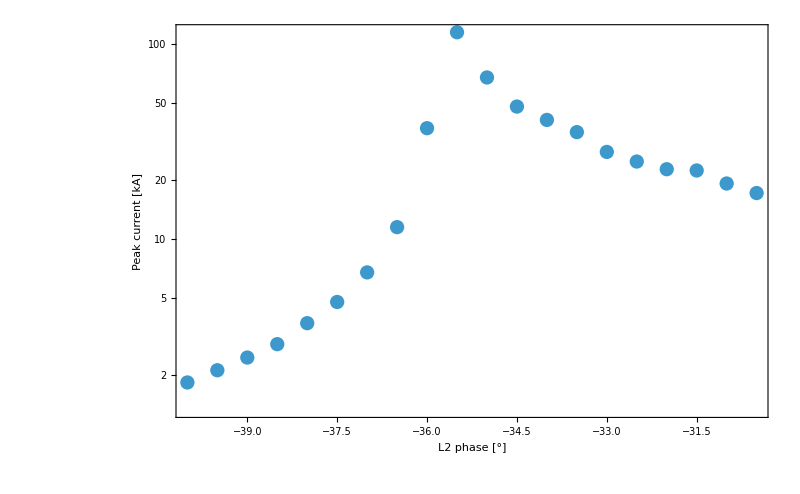

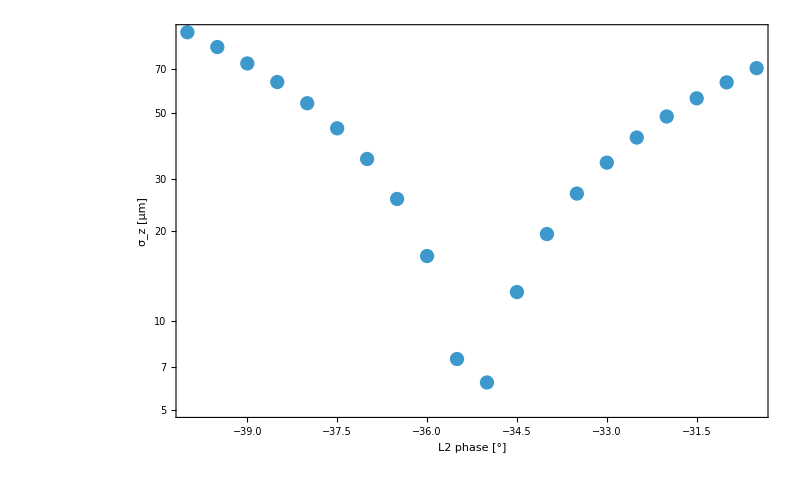

```mathematica
ListLogPlot[raw[[All,{1,2}]],ImageSize->800,LabelStyle->20,Frame->True,FrameLabel->{"L2 phase [°]","Peak current [kA]"}]
ListLogPlot[raw[[All,{1,3}]],ImageSize->800,LabelStyle->20,Frame->True,FrameLabel->{"L2 phase [°]","σ_z [μm]"}]
```

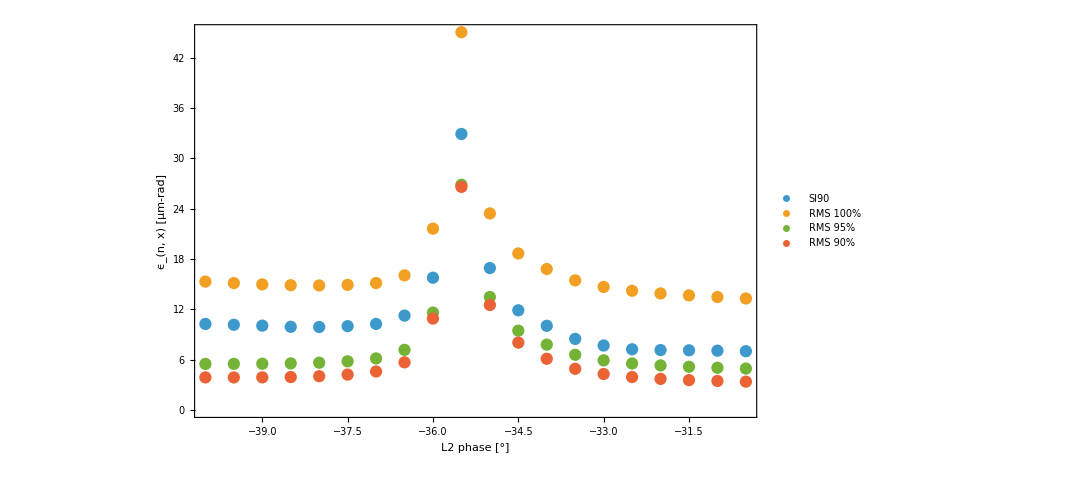

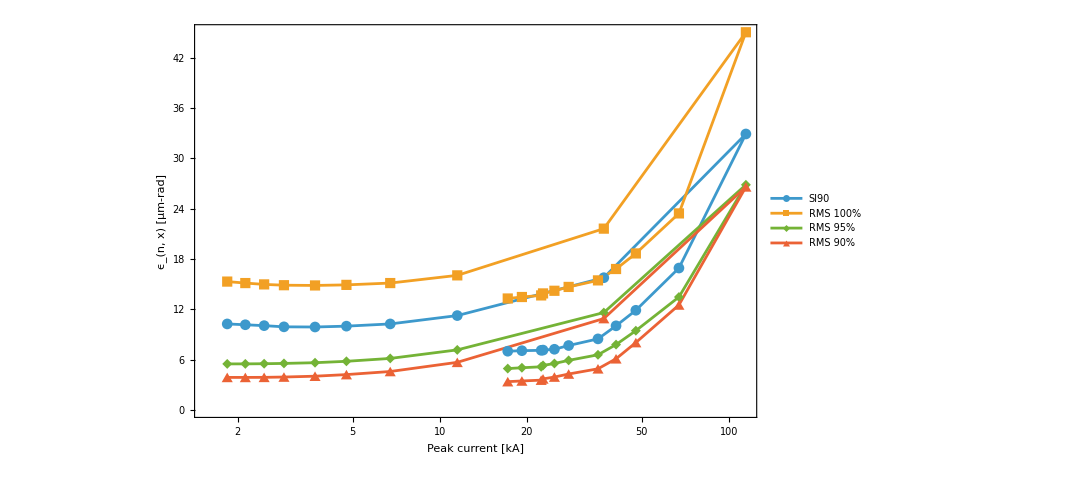

```mathematica
ListPlot[{
raw[[All,{1,4}]],
raw[[All,{1,5}]],
raw[[All,{1,6}]],
raw[[All,{1,7}]]
},
PlotLegends->Placed[{"SI90","RMS 100%","RMS 95%","RMS 90%"},{0.1,0.8}],
ImageSize->800,
LabelStyle->20,
Frame->True,
FrameLabel->{"L2 phase [°]","ϵ_(n, x) [μm-rad]"},
PlotRange->All
]

ListLogLinearPlot[{
raw[[All,{2,4}]],
raw[[All,{2,5}]],
raw[[All,{2,6}]],
raw[[All,{2,7}]]
},
PlotLegends->Placed[{"SI90","RMS 100%","RMS 95%","RMS 90%"},{0.1,0.8}],
ImageSize->800,
LabelStyle->20,
Frame->True,
FrameLabel->{"Peak current [kA]","ϵ_(n, x) [μm-rad]"},
Joined->True,
PlotMarkers->Automatic,
PlotRange->All
]
```

```mathematica
tmp = ListLinePlot3D[raw[[All,{1,2,4}]],ScalingFunctions->{None,"Log",None},PlotRange->All,SphericalRegion->True,ImageSize->800,LabelStyle->20,BoxRatios->{1, 1, 1},LabelStyle->20,
AxesLabel->{"L2 phase [°]","Peak current [kA]","SI90 ϵ_(n, x) [μm-rad]"},PlotMarkers->Automatic]
```

-Graphics3D-